# Analysis of a Referential Communication Task

## Thomas Gaul

## Initialisation

```mathematica
(* If you haven't already, download Dynamica from https://rdbeer.pages.iu.edu 
and put it in a folder that Mathematica can find *)
```

```mathematica
Get["Dynamica`"];
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

### Definitions for Loading Phenotype

```mathematica
$ParentDirectory = FileNameJoin[{NotebookDirectory[],"..","EvoP2"}];
SetDirectory[$ParentDirectory];
fileName[pop_]:=FileNameJoin[{StringJoin["Pop-",ToString[pop]],"phenotype.dat"}];
SetPhenotype[pop_]:=Module[{data,taus,thetas,weights,sensorweights},data=Flatten[Import[fileName[pop],"Table"]];
taus=data[[1;;5]];
thetas=data[[6;;10]];
weights=Partition[data[[11;;35]],5];
sensorweights=data[[36;;]];
CTRNN5y/.{
τ1->taus[[1]],τ2->taus[[2]],τ3->taus[[3]],τ4->taus[[4]],τ5->taus[[5]],
θ1->thetas[[1]],θ2->thetas[[2]],θ3->thetas[[3]],θ4->thetas[[4]],θ5->thetas[[5]],
w11->weights[[1,1]],w21->weights[[2,1]],w31->weights[[3,1]],w41->weights[[4,1]],w51->weights[[5,1]],
w12->weights[[1,2]],w22->weights[[2,2]],w32->weights[[3,2]],w42->weights[[4,2]],w52->weights[[5,2]],
w13->weights[[1,3]],w23->weights[[2,3]],w33->weights[[3,3]],w43->weights[[4,3]],w53->weights[[5,3]],
w14->weights[[1,4]],w24->weights[[2,4]],w34->weights[[3,4]],w44->weights[[4,4]],w54->weights[[5,4]],
w15->weights[[1,5]],w25->weights[[2,5]],w35->weights[[3,5]],w45->weights[[4,5]],w55->weights[[5,5]],
sw1->sensorweights[[1]],sw2->sensorweights[[2]],sw3->sensorweights[[3]],sw4->sensorweights[[4]],sw5->sensorweights[[5]]
}
];
```

### CTRNN Definitions

```mathematica
σ[x_]:=1/(1+ⅇ^-x);
```

#### 5-Dimensional System

```mathematica
(* if the following cell takes to long, edit Dynamica.m and lower the
$DynamicaSymbolicThreshold (the default is 5). Use this line to verify. *)
$DynamicaSymbolicThreshold
```

4

```mathematica
CTRNN5y=DynamicalSystem[
{
(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+w31 σ[y3+θ3]+w41 σ[y4+θ4]+w51 σ[y5+θ5]+sw1 d)/τ1,
(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2]+w32 σ[y3+θ3]+w42 σ[y4+θ4]+w52 σ[y5+θ5]+sw2 d)/τ2,
(-y3+w13 σ[y1+θ1]+w23 σ[y2+θ2]+w33 σ[y3+θ3]+w43 σ[y4+θ4]+w53 σ[y5+θ5]+sw3 d)/τ3,
(-y4+w14 σ[y1+θ1]+w24 σ[y2+θ2]+w34 σ[y3+θ3]+w44 σ[y4+θ4]+w54 σ[y5+θ5]+sw4 d)/τ4,
(-y5+w15 σ[y1+θ1]+w25 σ[y2+θ2]+w35 σ[y3+θ3]+w45 σ[y4+θ4]+w55 σ[y5+θ5]+sw5 d)/τ5
},
{{y1,-35,35},{y2,-35,35},{y3,-35,35},{y4,-35,35},{y5,-35,35}},
{
{θ1,-16,16},{θ2,-16,16},{θ3,-16,16},{θ4,-16,16},{θ5,-16,16},
{τ1,1,30},{τ2,1,30},{τ3,1,30},{τ4,1,30},{τ5,1,30},
{sw1,-16,16},{sw2,-16,16},{sw3,-16,16},{sw4,-16,16},{sw5,-16,16},
{w11,-16,16},{w21,-16,16},{w31,-16,16},{w41,-16,16},{w51,-16,16},
{w12,-16,16},{w22,-16,16},{w32,-16,16},{w42,-16,16},{w52,-16,16},
{w13,-16,16},{w23,-16,16},{w33,-16,16},{w43,-16,16},{w53,-16,16},
{w14,-16,16},{w24,-16,16},{w34,-16,16},{w44,-16,16},{w54,-16,16},
{w15,-16,16},{w25,-16,16},{w35,-16,16},{w45,-16,16},{w55,-16,16},
{d,0,1}
}
];
```

#### 2-Dimensional Reduction in State Space

```mathematica
CTRNN2y=DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+w41 +sw1 d)/τ1,
(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2]+w42 +sw2 d)/τ2},
{{y1,-35,35},{y2,-35,35}},
{
{w11,-16,16},{w21,-16,16},{w12,-16,16},{w22,-16,16},
{w41,-16,16},{w42,-16,16},
{sw1,-16,16},{sw2,-16,16},
{τ1,1,30},{τ2,1,30},
{θ1,-16,16},{θ2,-16,16},
{d,0,1}
}
];
```

### Loading Agent Phenotype

```mathematica
(* using agent 1 for most analysis *)
A = SetPhenotype[1];
A2d=CTRNN2y/.((#->DSParameterValue[A,#])&/@{
w11,w21,w12,w22,w41,w42,
sw1,sw2,
τ1,τ2,
θ1,θ2
}
);
```

### Transformation of Reduced Form to Output Space

```mathematica
With[{ε=10^-5},
Ao2d=TransformDynamicalSystem[A2d,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]
];
```

## Phase Plane Analysis

### Time Scale in 5D System

```mathematica
(* Time-constants *)
Print[#]&/@Table[A[[9,i]],{i,-5,-1}];
```

τ1→29.98083099999999845408638066147

τ2→16.65731604999999859728632145561

τ3→2.053627999999999786950866109692

τ4→29.96783899999999789542926009744

τ5→6.260788500000000311729309032671

```mathematica
A2d[[9]]
```

{sw1→15.98420800000000063789684645599,sw2→-4.954399999999999693045538151637,w11→9.382272000000000389263732358813,w12→-6.768112000000000350041773344856,w21→9.417232000000000269324118562508,w22→9.298944000000000542627276445273,w41→1.74254400000000009285372470913,w42→-13.63199999999999967315034155035,θ1→-14.31955199999999983617726684315,θ2→15.19025599999999975864284351701,τ1→29.98083099999999845408638066147,τ2→16.65731604999999859728632145561}

#### Timescale near saddle manifold

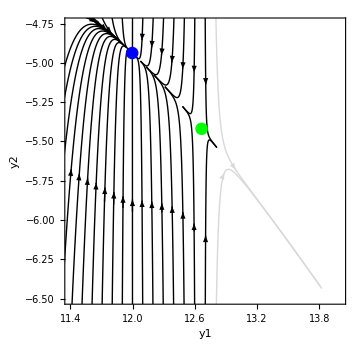

```mathematica
flow=Flatten[Table[{12+i,-4.9-j},{i,-1,.7,.1},{j,-.2,2,2.1}],1];
window={{11.4,14},{-6.5,-4.75}};
SaddlePoint=EquilibriumPoints[A/.{d->0}][[2,3]];
Show[
DisplayTrajectories[A2d/.{d->0},flow,145,StateVariables->{y1,y2},PlotRange->window,Arrows->1,PlotStyle->Black,FrameLabel->{"",""},LabelStyle->{FontSize->14},FrameTicksStyle->Directive[FontFamily->"Latin Modern Math",FontSize->12]
],
DisplayTrajectories[A2d/.{d->0},{{12.8,-4.6},{12.8,-6.9}},145,StateVariables->{y1,y2},PlotRange->window,Arrows->1,PlotStyle->LightGray],
DisplayPhasePortrait[A2d/.{d->0},StateVariables->{y1,y2},Tries->100,PlotRange->window],
ImageSize->Medium
]
```

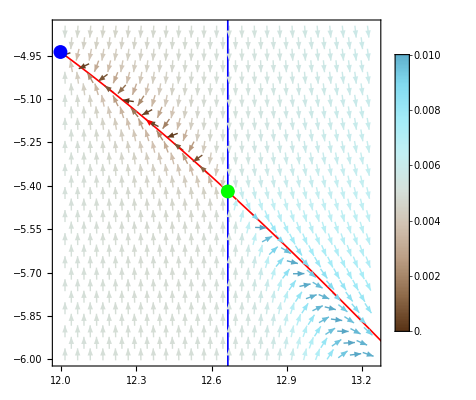

```mathematica
bounds={{11.99,13.25},{-6,-4.85}};
{dy1L,dy1U}=#[{Abs[A2d[[2,1]]/.Join[A2d[[9]],{d->0}]],bounds[[1,1]]<y1<bounds[[1,2]],bounds[[2,1]]<y2<bounds[[2,2]]},{y1,y2}]&/@{MinValue,MaxValue};
Show[
VectorPlot[A2d[[2]]/.Join[A2d[[9]],{d->0}],{y1,Sequence@@bounds[[1]]},{y2,Sequence@@bounds[[2]]}
,VectorPoints->Fine
,VectorColorFunction->Function[{x,y,vx,vy,n},ColorData["BrownCyanTones"][vx]]
,VectorColorFunctionScaling->{False,False,True,False,False}
,PlotLegends->Placed[BarLegend[
{ColorData[{"BrownCyanTones",{dy1L,dy1U}}][#]&,{dy1L,dy1U}},
LegendLabel->"",
LegendMarkerSize->275,
LegendMargins->0,
LabelStyle->Directive[FontFamily->"Latin Modern Math",FontSize->12]
],Right]
,FrameLabel->{"",""}
,LabelStyle->{FontSize->14}
,FrameTicksStyle->Directive[FontFamily->"Latin Modern Math",FontSize->12]
]
,Quiet[DisplayPhasePortrait[A2d/.{d->0},Tries->300
,SaddleManifolds->True
,SaddleManifoldPlotPoints->1000
,SaddleManifoldDuration->5000
]]
]
```

### Reduced Form in State Space

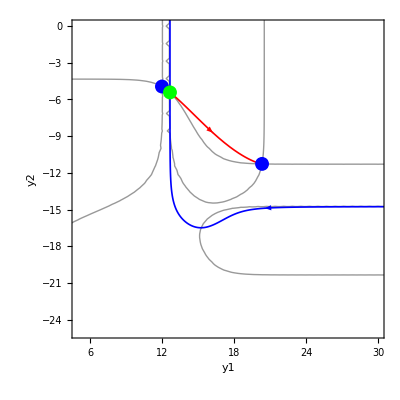

```mathematica
(* ignore error messages from `NDSolve` *)
Quiet[DisplayPhasePortrait[A2d/.{d->0},Tries->300,PlotRange->{{5,30},{-25,0}},
NullManifolds->True,
SaddleManifolds->True,
SaddleManifoldPlotPoints->1000,
SaddleManifoldDuration->5000,
FrameLabel->{"",""},
LabelStyle->{FontSize->14},
FrameTicksStyle->Directive[FontFamily->"Latin Modern Math",FontSize->12]
]]
```

### Reduced Form in Output-Space

#### Phase Portrait

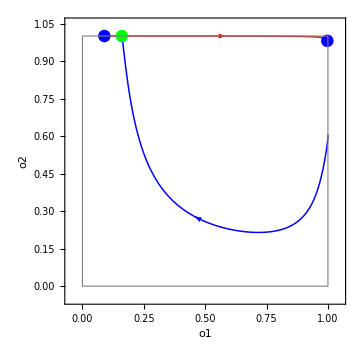

```mathematica
Show[
(* ignore error messages from `DisplayPhasePortrait` *)
Quiet[DisplayPhasePortrait[Ao2d/.{d->0}
,Tries->300,PlotRange->{{-.05,1.05},{-.05,1.05}}
,SaddleManifolds->True
,SaddleManifoldDuration->1000
,SaddleManifoldPlotPoints->1000
,NullManifolds->False
,FrameLabel->{"",""}
,LabelStyle->{FontSize->14}
,FrameTicksStyle->Directive[FontFamily->"Latin Modern Math",FontSize->12]
]]
,Graphics[{EdgeForm[{Thin,Gray,Dashed}],FaceForm[],Rectangle[{0,0},{1,1}]}]
,ImageSize->Medium
]
```

#### Step-Points

```mathematica
p1Phase1=Flatten[Import[FileNameJoin[{NotebookDirectory[],"p1_phase1.txt"}],"Table"]];
p1Phase2=Flatten[Import[FileNameJoin[{NotebookDirectory[],"p1_phase2.txt"}],"Table"]];
p2Phase3=Flatten[Import[FileNameJoin[{NotebookDirectory[],"p2_phase3.txt"}],"Table"]];
```

```mathematica
(* Subscript[N, 2] must be approximated due to saturation in output *)
SaddlePoint=EquilibriumPoints[A2d/.{d->0},Tries->300][[2,3]];
Attractor=EquilibriumPoints[A2d/.{d->0},Tries->300][[1,3]];
(* linear approximation to unstable saddle manifold *)
m=(Attractor[[2]]-SaddlePoint[[2]])/(Attractor[[1]]-SaddlePoint[[1]]);
b=SaddlePoint[[2]]-m*SaddlePoint[[1]];
Subscript[σ, -1][x_]:=Log[x/(1-x)]-θ1/.A2d[[9]];
StateFromOut[x_]:={Subscript[σ, -1][x],m Subscript[σ, -1][x]+b};
```

```mathematica
(* manually correcting points to land on transient/manifold *)
p1Phase2Traj=Thread[StateFromOut[p1Phase2]];
p1Phase2Traj = (p1Phase2Traj+{{0,0},{0,-.06},{0,.005},{0,.005}});
```

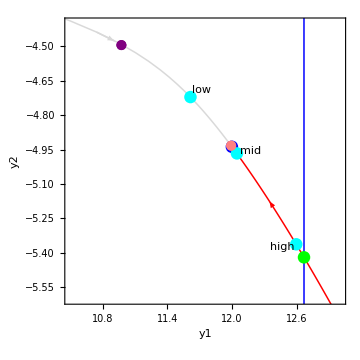

```mathematica
Show[
DisplayTrajectories[A2d/.{d->0},{{0,0}},1000,
PlotStyle->{LightGray,Thickness[.003]},Arrows->10,PlotRange->{{10.5,13},{-5.6,-4.4}},FrameLabel->{"",""},
LabelStyle->{FontSize->14},
FrameTicksStyle->Directive[FontFamily->"Latin Modern Math",FontSize->12]]
,Quiet[DisplayPhasePortrait[A2d/.{d->0},Tries->300
,SaddleManifolds->True
,SaddleManifoldDuration->1500,
SaddleManifoldPlotPoints->1000,
SaddleManifoldArrows->1,
MaxIterations->1000
]]
,ListPlot[p1Phase2Traj,PlotStyle->{Cyan,PointSize[0.025]}]
,ListPlot[{StateFromOut[p1Phase1[[1]]]-{0,.295}},PlotStyle->{Purple,PointSize[0.02]}]
,ListPlot[{StateFromOut[p2Phase3[[1]]]},PlotStyle->{Pink,PointSize[0.02]}]
,Graphics[Text[Framed[Style["low",Black,Italic,12,FontFamily->"Latin Modern Roman"],
Background->None,FrameStyle->None],p1Phase2Traj[[2]]+{.1,.03}]]
,Graphics[Text[Framed[Style["mid",Black,Italic,12,FontFamily->"Latin Modern Roman"],
Background->None,FrameStyle->None],p1Phase2Traj[[3]]+{.13,.01}]]
,Graphics[Text[Framed[Style["high",Black,Italic,12,FontFamily->"Latin Modern Roman"],
Background->None,FrameStyle->None],p1Phase2Traj[[4]]+{-.13,-.01}]]
,ImageSize->Medium
]
```

#### Verifying Saddle-to-Unstable Reduction

```mathematica
saddle2D=EquilibriumPoints[A2d/.{d->.3},Tries->1000][[1,3]]
saddle5D=EquilibriumPoints[A/.{d->.3},Tries->1000][[1,3]]
```

{14.5137,-16.0347}

{14.5137,-16.0347,-11.4858,19.8771,-4.40929}

```mathematica
sys5D=A[[10]]/.A[[9]];
egv5D=Eigenvalues[sys5D/.Thread[A[[3]]->saddle5D]];
egv5D
```

{-0.486943+0. ⅈ,-0.159725+0. ⅈ,0.0507392+0.0812506 ⅈ,0.0507392-0.0812506 ⅈ,-0.0333688+0. ⅈ}

```mathematica
egv2D=Eigenvalues[A2d[[10]]]/.A2d[[9]];
egv2D/.Thread[A2d[[3]]->saddle2D]
```

{0.0507393-0.0812506 ⅈ,0.0507393+0.0812506 ⅈ}

## Bifurcation Analysis

### Fixed Points

#### State-Space

```mathematica
DisplayBifurcationDiagram[A2d,d]
```

Warning: MaxSteps exceeded, terminating branch

Warning: MaxSteps exceeded, terminating branch

-Graphics3D-

#### Output-Space

```mathematica
DisplayBifurcationDiagram[Ao2d,d]
```

-Graphics3D-

### Bifurcation Diagrams With Limit-Cycle

#### Finding the limit cycle

LimitCycle[Stable,255.384,{0.967199,0.00265821}]

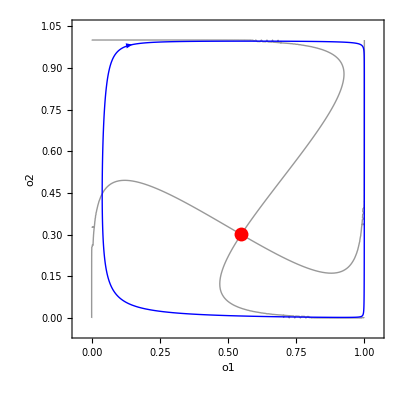

```mathematica
DisplayTrajectories[Ao2d/.{d->0.3},{{.99,.01}},270];
LC=FindLimitCycle[Ao2d/.{d->.3},Last[First[$Trajectories]],270]
Show[
DisplayPhasePortrait[Ao2d/.{d->0.3},Tries->300,SaddleManifolds->True,SaddleManifoldDuration->10000,SaddleManifoldPlotPoints->1000,NullManifolds->True,AccuracyGoal->10,PlotRange->{{-.05,1.05},{-.05,1.05}},
LimitSets->{LC}]
]
LCB=FollowLimitCycleBranch[LC,d,MaxStepSize->0.01];
```

#### Bifurcation Diagram in Output Space

```mathematica
Show[
DisplayBifurcationDiagram[Ao2d,d,Tries->300,MaxStepSize->0.01,LimitCycleBranches->{LCB},
BifurcationPointStyle->{PointSize[0.012]},ViewPoint->{1.110396031150695,1.6853439215169146,1.0847287772576018},
AxesLabel->{"","",""},
AxesStyle->Directive[FontSize->15],
(* `TicksStyle` option must be added in Dynamica.m; otherwise, remove the following line.
	An error may still be thrown, even if it works. If this bothers you too much, wrap this `DisplayBifurcationDiagram` function in a `Quiet` function.
*)
TicksStyle->Directive[FontFamily->"Latin Modern Math",FontSize->12]
],ImageSize->Medium
]
BPs=$BifurcationDiagramBPs;
```

DisplayBifurcationDiagram::optx: Unknown option {TicksStyle} in {Tries→300,MaxStepSize→0.01,LimitCycleBranches→{{«1»}},«1»,«1»,AxesLabel→{\*TemplateBox[<|"boxes" -> FormBox[StyleBo…tate" -> "Boxes"|>,"TeXAssistantTemplate"]\),…,…},AxesStyle→Directive[FontSize→15],TicksStyle→Directive[FontFamily→Latin Modern Math,FontSize→12]}.

-Graphics3D-

```mathematica
(* closeup of first bifurcation *)
Show[
DisplayBifurcationDiagram[Ao2d,d,Tries->300,BifurcationPointStyle->{PointSize[0.015]},MaxStepSize->0.001,
AxesLabel->{"","",""},
AxesStyle->Directive[FontSize->15],
(* `TicksStyle` option must be added in Dynamica.m; otherwise, remove the following line.
	An error may still be thrown, even if it works. If this bothers you too much, wrap this `DisplayBifurcationDiagram` function in a `Quiet` function.
*)
TicksStyle->Directive[FontFamily->"Latin Modern Math",FontSize->12],
Ticks->{{0,0.005},{0.05,0.1,0.15},{0.98,0.99}},
PlotRange->{{0.0,0.005},{0.05,0.2},{0.97,1.0}},BoxRatios->{1,2,1},
ViewPoint->{1.4284878636156926,1.4749015107756438,1.0169011540038673}
]
,ImageSize->Medium
]
```

Warning: MaxSteps exceeded, terminating branch

DisplayBifurcationDiagram::optx: Unknown option {TicksStyle} in {Tries→300,BifurcationPointStyle→{PointSize[0.015]},MaxStepSize→0.001,«4»,PlotRange→{{0.,0.005},{0.05,0.2},{0.97,1.}},BoxRatios→{1,2,1},ViewPoint→{1.42849,1.4749,1.0169}}.

-Graphics3D-

```mathematica
(* local bifurcations *)
Print[#]&/@BPs[[;;,1,9,1]];
```

d→0.0026083188445698

d→0.060307878365574

d→0.198362269242047

d→0.198368179321409

d→0.393890184938678

d→0.509887737709727

#### Global Bifurcations

```mathematica
Print[#]&/@BPs[[{3,4,5},1,9,1]];
```

d→0.198362269242047

d→0.198368179321409

d→0.393890184938678

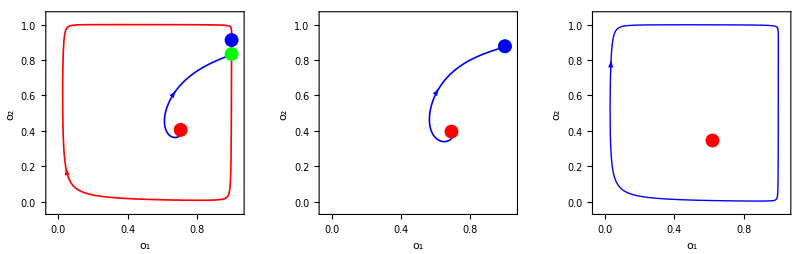

```mathematica
(* phase-portraits near first global-bifurcation *)
GraphicsRow[
Module[{},
DisplayTrajectories[Ao2d/.{d->#},{{.99,.01}},270];
Quiet[DisplayPhasePortrait[Ao2d/.{d->#},Tries->300,PlotRange->{{-.05,1.05},{-.05,1.05}},FrameLabel->{"o_1","o_2"},
SaddleManifolds->True,
SaddleManifoldDuration->1000,
SaddleManifoldPlotPoints->1000,
NullManifolds->False,
LimitSets->{FindLimitCycle[Ao2d/.{d->#},Last[First[$Trajectories]],270]}
]
]]&/@Table[BPs[[4,1,9,1,2]]+dd,{dd,{-0.01,0,0.05}}]
]
```

### Quasi-static Approximation

```mathematica
traj1=Import[FileNameJoin[{NotebookDirectory[],"naTraj1.txt"}],"Table"];
traj2=Import[FileNameJoin[{NotebookDirectory[],"naTraj2.txt"}],"Table"];
```

```mathematica
GraphicsGrid[
Table[
Show[
DisplayBifurcationDiagram[Ao2d,d,Tries->300,LimitCycleBranches->{LCB},StateVariables->{If[i===3,o1,o2]},MaxStepSize->0.01,BifurcationPointStyle->{PointSize[0.01]}],
ListLinePlot[{Drop[traj,0,{i}]},PlotStyle->Brown]
]
,{i,{3,2}},{traj,{traj1,traj2}}
]
]
```

-Graphics-

## Interaction Graphs

#### Interaction Graph for Receiver in Phase 3

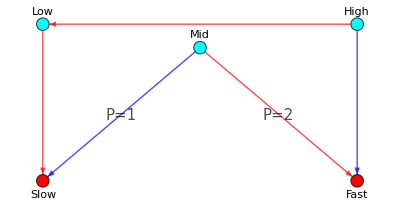

```mathematica
With[{c=Black},
GraphPlot[{Style[1->4,Red],Style[2->4,Blue],Style[2->5,Red],Style[3->5,Blue],Style[3->1,Red]},
DirectedEdges->True,EdgeStyle->Thick,
EdgeLabels->{
(2->4)->Style["P=1",Italic,FontSize->15,FontColor->c,FontFamily->"Latin Modern Math"],(2->5)->Style["P=2",Italic,FontSize->15,FontColor->c,FontFamily->"Latin Modern Math"]
},
VertexStyle->{1->Cyan,2->Cyan,3->Cyan,4->Red,5->Red},VertexSize->.08,
VertexCoordinates->{1->{1,2},2->{2,1.85},3->{3,2},4->{1,1},5->{3,1}},
VertexLabels->{
1->Placed[Style["Low",FontColor->c],Above],2->Placed[Style["Mid",FontColor->c],Above],3->Placed[Style["High",FontColor->c],Above],4->Placed[Style["Slow",FontColor->c],Below],5->Placed[Style["Fast",FontColor->c],Below]
}
]
]
```

### Complete Interaction Graph with Redundant Edges

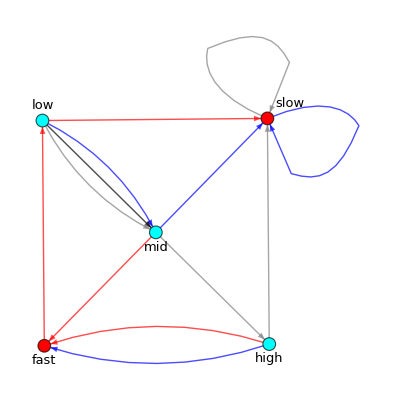

```mathematica
GraphPlot[
{Style[1->2,Blue],Style[1->4,Red],Style[1->2,Black],Style[1->2,Gray], Style[2->4,Blue],Style[2->3,Gray],Style[2->5,Red],Style[3->4,Gray],Style[3->5,Blue],Style[3->5,Red],Style[4->4,Gray],Style[4->4,Blue],Style[5->1,Red]},
DirectedEdges->True,EdgeStyle->Thick,
VertexStyle->{1->Cyan,2->Cyan,3->Cyan,4->Red,5->Red},VertexSize->.08,
VertexLabels->{
1->Placed[Style["low",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Above],2->Placed[Style["mid",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below],3->Placed[Style["high",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below],4->Placed[Style["slow",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],{After,Above}],5->Placed[Style["fast",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below]
}
]
```

```mathematica
Export["/home/tom/Documents/Work/Referential Communication/Preprint/Gaul.fig8a.pdf",%53,"PDF"]
```

/home/tom/Documents/Work/Referential Communication/Preprint/Gaul.fig8a.pdf

#### Unravelling the graph for the receiver in

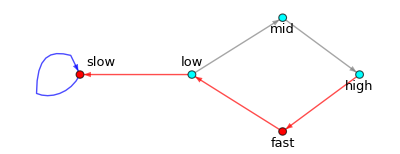

```mathematica
GraphPlot[
{Style[1->2,Gray],Style[2->3,Gray],Style[3->5,Red],Style[5->1,Red],Style[1->4,Red],Style[4->4,Blue]},
DirectedEdges->True,EdgeStyle->Thick,
VertexStyle->{1->Cyan,2->Cyan,3->Cyan,4->Red,5->Red},VertexSize->.08,
VertexLabels->{
1->Placed[Style["low",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Above],2->Placed[Style["mid",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below],3->Placed[Style["high",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below],4->Placed[Style["slow",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],{After,Above}],5->Placed[Style["fast",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below]
}
]
```

### Interaction Graph with Perturbation Classes

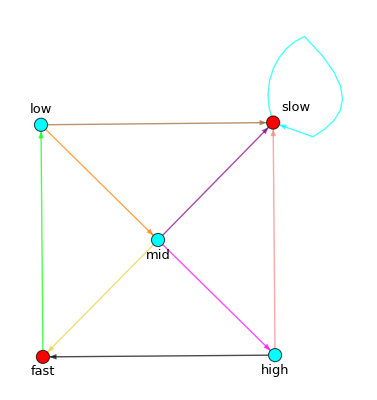

```mathematica
GraphPlot[
{Style[1->2,Orange],Style[1->4,Brown], Style[2->4,Purple],Style[2->3,Magenta],
Style[2->5,RGBColor[0.9211163550040478, 0.8162447051330659, 0.2590925803004436]],Style[3->4,Pink],Style[3->5,Black],Style[4->4,Cyan],Style[5->1,Green]},
DirectedEdges->True,EdgeStyle->Thick,
VertexStyle->{1->Cyan,2->Cyan,3->Cyan,4->Red,5->Red},VertexSize->.08,
VertexLabels->{
1->Placed[Style["low",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Above],2->Placed[Style["mid",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below],3->Placed[Style["high",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below],4->Placed[Style["slow",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],{After,Above}],5->Placed[Style["fast",FontColor->Black,FontFamily->"Latin Modern Roman",Italic,FontSize->13],Below]
}
]
```

```mathematica
Export["/home/tom/Documents/Work/Referential Communication/Preprint/Gaul.fig8b.pdf",%55,"PDF"]
```

/home/tom/Documents/Work/Referential Communication/Preprint/Gaul.fig8b.pdf

## Phase Portraits for Additional Agents

### Agent 2 (Step-Type)

```mathematica
A2=SetPhenotype[2];
```

```mathematica
(* Coordinates of first equilibrium point *)
equ2=EquilibriumPoints[A2/.{d->0}][[1,3]];
(* generating flow grid *)
flow2=Flatten[Table[Join[{equ2[[1]]},{i,j},equ2[[4;;]]],{i,-35,35,5},{j,-35,35,5}],1];
Length[flow2]
```

225

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 38.1328 and t = 38.5064.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 152.086 and t = 152.277.

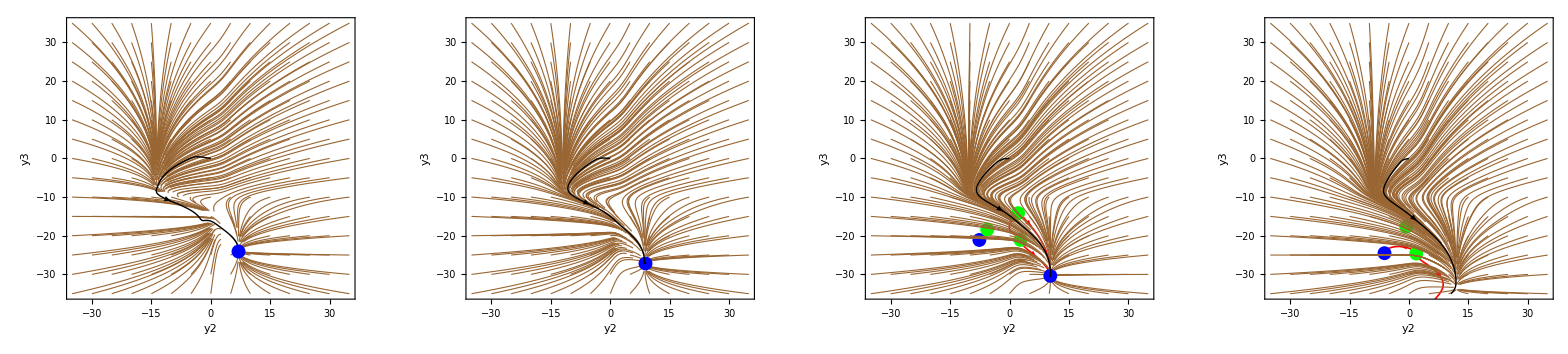

```mathematica
With[{i=0,j=.25,k=.5,l=.75},
GraphicsRow[{
Show[
DisplayPhasePortrait[A2/.{d->i},StateVariables->{y2,y3},SaddleManifolds->True],
DisplayTrajectories[A2/.{d->i},flow2,20,StateVariables->{y2,y3},Arrows->0],
DisplayTrajectories[A2/.{d->i},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y3},PlotStyle->Black]
],
Show[
DisplayPhasePortrait[A2/.{d->j},StateVariables->{y2,y3},SaddleManifolds->True],
DisplayTrajectories[A2/.{d->j},flow2,20,StateVariables->{y2,y3},Arrows->0],
DisplayTrajectories[A2/.{d->j},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y3},PlotStyle->Black]
],
Show[
DisplayPhasePortrait[A2/.{d->k},StateVariables->{y2,y3},SaddleManifolds->True],
DisplayTrajectories[A2/.{d->k},flow2,20,StateVariables->{y2,y3},Arrows->0],
DisplayTrajectories[A2/.{d->k},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y3},PlotStyle->Black]
],
Show[
DisplayPhasePortrait[A2/.{d->l},StateVariables->{y2,y3},SaddleManifolds->True],
DisplayTrajectories[A2/.{d->l},flow2,20,StateVariables->{y2,y3},Arrows->0],
DisplayTrajectories[A2/.{d->l},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y3},PlotStyle->Black]
]
}]
]
```

### Agent 3 (Basin-Type)

```mathematica
A3=SetPhenotype[3];
```

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A3/.{d->i},StateVariables->{y2,y4,y5},SaddleManifolds->True,SaddleManifoldDuration->1000,SaddleManifoldPlotPoints->1000,Tries->200],
DisplayTrajectories[A3/.{d->i},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y4,y5}]
]
]
```

-Graphics3D-

### Agent 4 (Basin-Type)

```mathematica
A4=SetPhenotype[4];
```

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A4/.{d->i},StateVariables->{y1,y2,y5},SaddleManifolds->True,SaddleManifoldDuration->1000,SaddleManifoldPlotPoints->1000,Tries->200],
DisplayTrajectories[A4/.{d->i},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y1,y2,y5}]
]
]
```

-Graphics3D-

### Agent 5 (Step-Type)

```mathematica
A5=SetPhenotype[5];
```

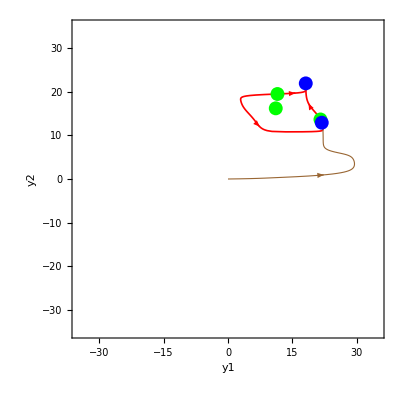

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A5/.{d->i},Tries->300,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2}],
DisplayTrajectories[A5/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2}]
]
]
```

### Agent 6 (Step-Type)

```mathematica
A6=SetPhenotype[6];
```

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A6/.{d->i},Tries->300,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2,y5}],
DisplayTrajectories[A6/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2,y5}]
]
]
```

-Graphics3D-

### Agent 7 (Basin-Type)

```mathematica
A7=SetPhenotype[7];
```

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A7/.{d->i},Tries->300,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2,y4}],
DisplayTrajectories[A7/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2,y4}]
]
]
```

-Graphics3D-

### Agent 8 (Step-Type)

```mathematica
A8=SetPhenotype[8];
```

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A8/.{d->i},Tries->300,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2,y3}],
DisplayTrajectories[A8/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2,y3}]
]
]
```

-Graphics3D-

### Agent 9 (Basin-Type)

```mathematica
A9=SetPhenotype[9];
```

```mathematica
flow9=Tuples[{-35,35},5];
Length[flow9]
```

32

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A9/.{d->i},Tries->500,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2,y5}],
DisplayTrajectories[A9/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2,y5},PlotStyle->Black],
DisplayTrajectories[A9/.{d->i},flow9,500,PlotPoints->1000,StateVariables->{y1,y2,y5}]
]
]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 307.599 and t = 308.414.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 294.115 and t = 294.475.

-Graphics3D-